```mathematica
Clear["Global`*"]
NotebookSave[]
(*https://mathematica.stackexchange.com/questions/38114/how-to-set-the-working-precision-globally-minprecision-does-not-work*)
SetOptions[SelectedNotebook[],PrintPrecision->40]
SetDirectory[NotebookDirectory[]];
```

## Lagrangian Setup

### Background Metric

Kerr-Newman-Taub-NUT variables

```mathematica
(*
sigma = r[L]^2 + (l+a*Cos[theta[L]])^2;
delta = r[L]^2-2*M*r[L]+a*a-l*l+Q*Q;
chi = a*Sin[theta[L]]^2 - 2*l*Cos[theta[L]];
*)
derivConv = {delta'[r_] :> 2.*r-2.*M,
Derivative[1,0][sigma][r_,theta_]:>2.*r,
Derivative[0,1][sigma][r_,theta_]:>2.*(l+a*Cos[theta])*-Sin[theta],
 chi'[theta_]:>a*Sin[2*theta] + 2.*l*Sin[theta]}
```

{delta'[r_]:>2. r-2. M,sigma^(1,0)[r_,theta_]:>2. r,sigma^(0,1)[r_,theta_]:>2. (l+a Cos[theta]) (-Sin[theta]),chi'[theta_]:>a Sin[2 theta]+2. l Sin[theta]}

Minkowski H. Raum und Zeit[Space and Time]. Physikalische Zeitschrift. (1908–1909)10:75–88.

```mathematica
minkowski = -t'[L]^2 + r'[L]^2 + r[L]^2*(theta'[L]^2 + Sin[theta[L]]^2*phi'[L]^2)
```

r'[L]^2-t'[L]^2+r[L]^2 (Sin[theta[L]]^2 phi'[L]^2+theta'[L]^2)

Schwarzschild K. Über das gravitationsfeld eines massenpunktes nach der einsteinschen theorie. Sitzungsberichte der königlich preussischen Akademie der Wissenschaften.1916:189-96.

```mathematica
schwarzschild = -(1 - 2*M/r[L])*t'[L]^2 + (1 - 2*M/r[L])^-1*r'[L]^2 + r[L]^2*(theta'[L]^2 + Sin[theta[L]]^2*phi'[L]^2)
```

r'[L]^2/(1-(2 M)/r[L])+(-1+(2 M)/r[L]) t'[L]^2+r[L]^2 (Sin[theta[L]]^2 phi'[L]^2+theta'[L]^2)

Reissner H. Über die Eigengravitation des elektrischen Feldes nach der Einsteinschen Theorie. Annalen der Physik. 1916, 355(9):106-20.

Weyl H. Zur gravitationstheorie. Annalen der physik. 1917, 359(18):117-45.

Nordström G. On the energy of the gravitation field in Einstein’s theory. Koninklijke Nederlandse Akademie van Wetenschappen Proceedings Series B Physical Sciences.1918 Jan, 20:1238-45.

Jeffery GB. The field of an electron on Einstein’s theory of gravitation. Proceedings of the Royal Society of London.Series A,Containing Papers of a Mathematical and Physical Character. 1921 May 2, 99(697):123-34.

```mathematica
RN = -(1 - 2*M/r[L]+Q^2)*t'[L]^2 + (1 - 2*M/r[L]+Q^2)^-1*r'[L]^2 + r[L]^2*(theta'[L]^2 + Sin[theta[L]]^2*phi'[L]^2)
```

r'[L]^2/(1+Q^2-(2 M)/r[L])+(-1-Q^2+(2 M)/r[L]) t'[L]^2+r[L]^2 (Sin[theta[L]]^2 phi'[L]^2+theta'[L]^2)

Kerr RP. Gravitational field of a spinning mass as an example of algebraically special metrics. Physical review letters. 1963 Sep 1,11(5):237.

```mathematica
kerr = -(1 - 2*M*r[L]/sigma[r[L],theta[L]])*t'[L]^2 + r'[L]^2*sigma[r[L],theta[L]] / delta[r[L]]+ sigma[r[L],theta[L]]*theta'[L]^2 + (r[L]^2 + a^2 + 2*M*r[L]*a^2/sigma[r[L],theta[L]]*Sin[theta[L]]^2)*Sin[theta[L]]^2*phi'[L]^2 - 4*M*r[L]*a*Sin[theta[L]]^2 / sigma[r[L], theta[L]]*t'[L]*phi'[L] /.{theta[L]->Pi/2}
(*Plane constraining^ (add /.{theta[L]->Pi/2})*)
```

(a^2+r[L]^2+(2 a^2 M r[L])/sigma[r[L],π/2]) phi'[L]^2+(sigma[r[L],π/2] r'[L]^2)/delta[r[L]]-(4 a M r[L] phi'[L] t'[L])/sigma[r[L],π/2]+(-1+(2 M r[L])/sigma[r[L],π/2]) t'[L]^2+sigma[r[L],π/2] theta'[L]^2

Newman ET, Couch E, Chinnapared K, Exton A, Prakash A, Torrence R. Metric of a rotating, charged mass. Journal of mathematical physics. 1965 Jun 1;6(6):918-9.

```mathematica
kerrNewman = -(r'[L]^2 / delta[r[L]] + theta'[L]^2)*sigma[r[L],theta[L]] + (t'[L] - a*Sin[theta[L]]^2*phi'[L])^2*delta[r[L]] / sigma[r[L],theta[L]] - ((r[L]^2 + a^2)*phi'[L] - a*t'[L])^2*Sin[theta[L]]^2/sigma[r[L],theta[L]]
```

(delta[r[L]] (-a Sin[theta[L]]^2 phi'[L]+t'[L])^2)/sigma[r[L],theta[L]]-(Sin[theta[L]]^2 ((a^2+r[L]^2) phi'[L]-a t'[L])^2)/sigma[r[L],theta[L]]+sigma[r[L],theta[L]] (-r'[L]^2/delta[r[L]]-theta'[L]^2)

Caution: if an expression with chi is included, its value cannot be zero, i.e., a*sin^2(theta) - 2*l*cos(theta) != 0

Cebeci H, Özdemir N, Şentorun S. Motion of the charged test particles in Kerr-Newman-Taub-NUT spacetime and analytical solutions. Physical Review D. 2016 May 15;93(10):104031.

```mathematica
focusBackground = -delta[r[L]]/sigma[r[L],theta[L]] * (t'[L]-chi[theta[L]]*phi'[L])^2 + sigma[r[L],theta[L]]*(r'[L]^2 / delta[r[L]] + theta'[L]^2) + Sin[theta[L]]^2/sigma[r[L],theta[L]]*(a*t'[L] - (r[L]*r[L]+l*l+a*a)*phi'[L])^2/. {l->0, theta[L]->Pi/2}
(*Plane and l constraining^ (add /.{chi[theta_]:>a, l->0, theta[L]->Pi/2})*)
```

-(delta[r[L]] (-chi[π/2] phi'[L]+t'[L])^2)/sigma[r[L],π/2]+((-((a^2+r[L]^2) phi'[L])+a t'[L])^2)/sigma[r[L],π/2]+sigma[r[L],π/2] (r'[L]^2/delta[r[L]]+theta'[L]^2)

```mathematica
background = kerrNewman;
(*https://mathematica.stackexchange.com/questions/263450/what-is-the-most-efficient-way-to-turn-a-metric-formula-into-a-metric-tensor*)
g = Last@CoefficientArrays[background,{t'[L],r'[L],phi'[L],theta'[L]}];

For[i=1,i<=4,i++,
For[j = 1, j<i, j++,
g[[j,i]] = g[[j,i]]/2;
g[[i,j]] = g[[j,i]]];
]

g//MatrixForm
```

(delta[r[L]]/sigma[r[L],theta[L]]-(a^2 Sin[theta[L]]^2)/sigma[r[L],theta[L]] | 0 | 1/2 (-(2 a delta[r[L]] Sin[theta[L]]^2)/sigma[r[L],theta[L]]+(2 a (a^2+r[L]^2) Sin[theta[L]]^2)/sigma[r[L],theta[L]]) | 0
0 | -sigma[r[L],theta[L]]/delta[r[L]] | 0 | 0
1/2 (-(2 a delta[r[L]] Sin[theta[L]]^2)/sigma[r[L],theta[L]]+(2 a (a^2+r[L]^2) Sin[theta[L]]^2)/sigma[r[L],theta[L]]) | 0 | -((a^2+r[L]^2)^2 Sin[theta[L]]^2)/sigma[r[L],theta[L]]+(a^2 delta[r[L]] Sin[theta[L]]^4)/sigma[r[L],theta[L]] | 0
0 | 0 | 0 | -sigma[r[L],theta[L]])

### Black Hole Electric Field

```mathematica
(*https://en.wikipedia.org/wiki/Relativistic_Lagrangian_mechanics#General_relativistic_test_particle_in_an_electromagnetic_field*)
electricBackground = 2.*q/m*Q*r[L]/sigma[r[L],theta[L]]*(-t'[L] + chi[theta[L]]*phi'[L])
(*Plane and l constraining^  (add /. chi[theta_]:>a)*)
```

(2. q Q r[L] (chi[theta[L]] phi'[L]-t'[L]))/(m sigma[r[L],theta[L]])

### Particle Pair Potential

```mathematica
(*Electric Field Second Particle*)

(*
n = {r[L]*Sin[theta[L]]*Cos[phi[L]] - sourceR[L]*Sin[sourceTheta[L]]*Cos[sourcePhi[L]], r[L]*Sin[theta[L]]*Sin[phi[L]]- sourceR[L]*Sin[sourceTheta[L]]*Sin[sourcePhi[L]], r[L]*Cos[theta[L]] - sourceR[L]*Cos[sourceTheta[L]]};
*)

norm[x_] := Sqrt[x.x]
n[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]] = {nx[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]],ny[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]],nz[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]]};
nUnit = n[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]] / norm[n[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]]];
potentialSource = 1./(4.*Pi*epsilon0)*q*q / (1. - Dot[nUnit,{sourceR'[L]*Sin[sourceTheta'[L]]*Cos[sourcePhi'[L]],sourceR'[L]*Sin[sourceTheta'[L]]*Sin[sourcePhi'[L]],sourceR'[L]*Cos[sourceTheta'[L]]}]) / norm[n[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]]];
LJ = 4.*epsilon*((sigma0/norm[n[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]]])^12 - (sigma0/norm[n[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]]])^6);

(*https://en.wikipedia.org/wiki/Li%C3%A9nard%E2%80%93Wiechert_potential*)

electricSource = Simplify[1./m*LJ*Sum[Sum[g[[i,j]]*{1, 0*sourceR'[L], 0*sourcePhi'[L], 0*sourceTheta'[L]}[[i]]*{t'[L], r'[L], phi'[L], theta'[L]}[[j]],{i,1,4}],{j,1,4}]]//. {(nx[r_,theta_,phi_,sourceR_,sourcePhi_,sourceTheta_]^2+ny[r_,theta_,phi_,sourceR_,sourcePhi_,sourceTheta_]^2+nz[r_,theta_,phi_,sourceR_,sourcePhi_,sourceTheta_]^2)^power_:>nmag[r,theta,phi,sourceR,sourcePhi,sourceTheta]^(2*power)} // Simplify
```

(4. epsilon sigma0^6 (sigma0^6-nmag[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]]^6) (a (a^2-delta[r[L]]+r[L]^2) Sin[theta[L]]^2 phi'[L]+(delta[r[L]]-a^2 Sin[theta[L]]^2) t'[L]))/(m nmag[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]]^12 sigma[r[L],theta[L]])

## Euler-Lagrange Equations

### Producing the E-L Equations

```mathematica
(*Euler-Lagrange equations*)
lagrangian = background + electricBackground + electricSource /. {theta[L]->Pi/2, sourceTheta[L]->Pi/2};
(*Plane constraining^ (add /. {theta[L]->Pi/2, sourceTheta[L]->Pi/2}) *)
Timing[sol= Table[
Simplify@D[D[lagrangian, D[i,L]], L]==Simplify@D[lagrangian, i], {i,{t[L], r[L], phi[L],theta[L]}}
];]
```

{0.15625,Null}

```mathematica
Timing[sol = (sol /. derivConv );]
```

{0.,Null}

### Format Equations of Motion

```mathematica
Timing[sol2 = #[[2]]&/@Solve[sol, {t''[L],r''[L],phi''[L],theta''[L]}][[1]] /. {theta'[L]->0,nz[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]]->0};]
(* Plane constraining^ (add /. {theta'[L]->0,nz[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]]->0})*)
```

{0.15625,Null}

```mathematica
Timing[sol3 = sol2 //.
{Derivative[n___][nmag][r_,theta_,phi_,sourceR_,sourcePhi_,sourceTheta_]:>(nx[r,theta,phi,sourceR,sourcePhi,sourceTheta]*Derivative[n][Function[{rT,thetaT,phiT,sourceRT,sourcePhiT,sourceThetaT},rT*Sin[thetaT]*Cos[phiT] - sourceRT*Sin[sourceThetaT]*Cos[sourcePhiT]]][r,theta,phi,sourceR,sourcePhi,sourceTheta] + ny[r,theta,phi,sourceR,sourcePhi,sourceTheta]*Derivative[n][Function[{rT,thetaT,phiT,sourceRT,sourcePhiT,sourceThetaT},
rT*Sin[thetaT]*Sin[phiT]- sourceRT*Sin[sourceThetaT]*Sin[sourcePhiT]]][r,theta,phi,sourceR,sourcePhi,sourceTheta] + nz[r,theta,phi,sourceR,sourcePhi,sourceTheta]*Derivative[n][Function[{rT,thetaT,phiT,sourceRT,sourcePhiT,sourceThetaT},rT*Cos[thetaT] - sourceRT*Cos[sourceThetaT]]][r,theta,phi,sourceR,sourcePhi,sourceTheta]) / nmag[r,theta,phi,sourceR,sourcePhi,sourceTheta],

Derivative[n___][nx][r_,theta_,phi_,sourceR_,sourcePhi_,sourceTheta_]:>Derivative[n][Function[{rT,thetaT,phiT,sourceRT,sourcePhiT,sourceThetaT},rT*Sin[thetaT]*Cos[phiT] - sourceRT*Sin[sourceThetaT]*Cos[sourcePhiT]]][r,theta,phi,sourceR,sourcePhi,sourceTheta],

Derivative[n___][ny][r_,theta_,phi_,sourceR_,sourcePhi_,sourceTheta_]:>Derivative[n][Function[{rT,thetaT,phiT,sourceRT,sourcePhiT,sourceThetaT},
rT*Sin[thetaT]*Sin[phiT]- sourceRT*Sin[sourceThetaT]*Sin[sourcePhiT]]][r,theta,phi,sourceR,sourcePhi,sourceTheta],

Derivative[n___][nz][r_,theta_,phi_,sourceR_,sourcePhi_,sourceTheta_]:>Derivative[n][Function[{rT,thetaT,phiT,sourceRT,sourcePhiT,sourceThetaT},rT*Cos[thetaT] - sourceRT*Cos[sourceThetaT]]][r,theta,phi,sourceR,sourcePhi,sourceTheta]} /.


{t'[L]->tdot, r'[L]->rdot, phi'[L]->phidot, theta'[L]->thetadot,sourceR'[L]->rsdot, sourcePhi'[L]->phisdot, sourceTheta'[L]->thetasdot,sourceR''[L]->rsddot, sourcePhi''[L]->phisddot, sourceTheta''[L]->thetasddot} /.

{t[L]->t,r[L]->r, phi[L]->phi,theta[L]->theta,sourceR[L]->rs, sourcePhi[L]->phis,sourceTheta[L]->thetas, nx[r_,theta_,phi_,sourceR_,sourcePhi_,sourceTheta_]:> nx, ny[r_,theta_,phi_,sourceR_,sourcePhi_,sourceTheta_]:> ny, nz[r_,theta_,phi_,sourceR_,sourcePhi_,sourceTheta_]:> nz, nmag[r_,theta_,phi_,sourceR_,sourcePhi_,sourceTheta_]:> nmag};]
```

{0.015625,Null}

```mathematica
Timing[output = Table[ToString@CForm@(sol3[[i]]), {i,1,4}];]
```

{0.,Null}

```mathematica
Export["src/eulerLagrange.cpp",StringRiffle[output,"\n"],"Text"]
```

src/eulerLagrange.cpp

## Kerr Orbital Velocities

```mathematica
lagrangian = kerr/. {theta[L]->Pi/2, sourceTheta[L]->Pi/2};
(*Plane constraining^ (add /. {theta[L]->Pi/2, sourceTheta[L]->Pi/2}) *)
Timing[sol= Table[
Simplify@D[D[lagrangian, D[i,L]], L]==Simplify@D[lagrangian, i], {i,{t[L], r[L], phi[L],theta[L]}}
];]
```

{0.,Null}

```mathematica
Timing[sol = (sol /. derivConv );]
```

{0.,Null}

```mathematica
Timing[sol2 = #[[2]]&/@Solve[sol, {t''[L],r''[L],phi''[L],theta''[L]}][[1]] /. {theta'[L]->0,nz[r[L],theta[L],phi[L],sourceR[L],sourcePhi[L],sourceTheta[L]]->0};]
```

{0.,Null}

```mathematica
eq=0 == sol2[[2]] /. {sigma[r_,theta_]:>r^2+a^2, r'[L]->0}
```

0==-(0.5 delta[r[L]] (0.-2. r[L] phi'[L]^2+(4. M r[L]^2 (-1. a phi'[L]+t'[L])^2)/((a^2+r[L]^2)^2)-(2. M (-1. a phi'[L]+t'[L])^2)/(a^2+r[L]^2)))/(a^2+r[L]^2)

```mathematica
sol3 = Solve[eq, phi'[L]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{phi'[L]→(a^3 M t'[L]-1. a M r[L]^2 t'[L]-1. √(-1. a^6 M r[L] t'[L]^2-1. a^4 M r[L]^3 t'[L]^2+a^2 M r[L]^5 t'[L]^2+M r[L]^7 t'[L]^2))/(a^4 M+a^4 r[L]-1. a^2 M r[L]^2+2. a^2 r[L]^3+r[L]^5)},{phi'[L]→(a^3 M t'[L]-1. a M r[L]^2 t'[L]+√(-1. a^6 M r[L] t'[L]^2-1. a^4 M r[L]^3 t'[L]^2+a^2 M r[L]^5 t'[L]^2+M r[L]^7 t'[L]^2))/(a^4 M+a^4 r[L]-1. a^2 M r[L]^2+2. a^2 r[L]^3+r[L]^5)}}

Choosing to look at + solution (velocity in direction of black hole rotation).

```mathematica
sol4=((sol3[[2,1,2]]*r[L]) /. {r[L]->r, t'[L]->1} // Simplify)
```

(1. a^3 M r-1. a M r^3+1. r √(M r (-1. a^6-1. a^4 r^2+a^2 r^4+r^6)))/(r^5+a^4 (M+r)+a^2 r^2 (-1. M+2. r))

```mathematica
vorb[r_, M_, a_]:=Evaluate@sol4
```

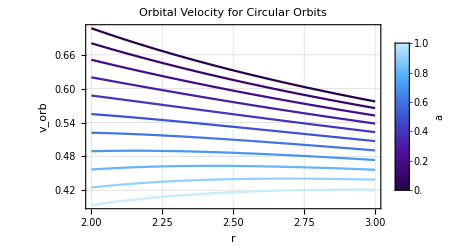

```mathematica
(*https://mathematica.stackexchange.com/questions/27783/is-it-possible-to-style-multiple-plot-or-listplot-curves-using-a-color-gradient*)
curves = Table[vorb[r, 1, a], {a, 0, 1, 0.1}];
barLegend = BarLegend[{"DeepSeaColors",{0,1}}, LegendLabel->"a", LegendMarkerSize->150];
Style[Plot[curves, {r, 2, 3},
 FrameLabel->(Style[#, FontSize->12]&/@ {"r", "v_orb"}),
PlotLabel->Style["Orbital Velocity for Circular Orbits", FontSize->16],
LabelStyle->Black,
Frame->True,
GridLines->Automatic,
PlotStyle->Table[ColorData["DeepSeaColors",i/(Length[curves]-1)],{i,0,Length[curves]-1}],
PlotLegends->Placed[barLegend, {After,Bottom}]], PrintPrecision->2]
```